# Oral Presentation Script

```mathematica
text ="My name is Yu Jie and I will be presenting my FYP
on the use of network mechanics for hydrogel fracture. 
In particular, community detection is applied to a
construction of a Delaunay network. This is to develop inhomogenous material properties 
for a hydrogel fracture simulation. This FYP is based on work done in Prof. Li's research group.
My role for the FYP is to find ways to compare the shape of the crack to known
experimental results which will be used in a future experimental study.

The following is a word cloud of the text in my FYP report for your interest.
The goal of this presentation is to: 
(1) describe the joint work done in Prof. Li's research group in mesoscopic
network mechanics. Mesoscopic refers to the region in between the microscopic
and macroscopic parameters. This was done by Dr. Lei Jincheng, Dr. Zheng Shoujing
and Dr. You Hao.
(2) describe the methods I come up with to extract the finite element
analysis results, and compare this with known experimental results.

For my FYP, the research group has already validated the stress-stretch characteristics
of a novel finite element simulation that was yet to be published with an existing mesoscopic
network model done by Dr Lei Jincheng in his 2021 paper published in the Journal of Mechanics
and Physics of Solids. However, it was also desired that the crack shape be 
validated with the experimental results. In the literature, there was a gap in terms 
of the validation of this sort of meandering crack.

Therefore, we can discuss the research gap in the literature.
For the meandering crack, there was barely any literature within mechanics that validates
this sort of crack. Therefore, a goal for this final year project is to conduct
a feasibility study. This feasibility study is to look for methods to 
compare the crack shape between experimental results and the simulation. This is to be done
before a full fledged experimental study is conducted.

Based on the first goal of this presentation, I will describe the basic construction of the 
mesoscopic network mechanics model. I will also describe how failure is simulated using phase field 
methods. The first step is to construct a Delaunay network. The network is scaled from the microscale
to the macroscale based on an assumption of Gaussian statistics. This simulates the microscopic 
inhomogenous local density of the polymer chains in a hydrogel.
Then, communities are detected based
on the network density. The communities are then assigned local material properties, using
methods in Lei's 2021 paper.
Lastly, a 2D fracture simulation is done based on a 
modified phase field method using a heat transfer analogy as done in Zheng 2022.

For the second goal of this presentation, several suitable measures were found
to compare the two cracks.
Firstly, a polynomial fit of the crack shapes was done for the simulation results and the
experiment. Secondly, several measures were calculated to compare the two cracks.
This includes the sinuosity, curvature, and the circular statistics of the plot. 
The curves are first discretised into various segments before these measures are calculated.
The sinuosity is the ratio of the total length of the crack to the straight line length of the crack.
The curvature (or 2D curvature for a unit speed parametised curve) intuitively measures how much 
a curve deviate from a straight line.
The mean angle and circular variance measures what the angle is between different segments of the curve.

To start with network mechanics, random points are drawn from a uniform distribution on the plane.
Then, an initial Delaunay trianglular network is constructed. Lastly, energy methods are used
to optimise this network to prevent distorted triangles. The triangular network shown here
that I did was achieved through brute force. Dr Lei used more sophisticated energy methods to 
perform the optimisation.

Then, these nodes represent the local density of hydrogel polymer chains, and a community detection
algorithm is applied. We start from a vertex and define a community from there. The complement of this
community that is in the structural neighbourhood (this means that is connected) is also defined.
Pick the vertex of the graph which is closest or has the highest similarity score. Then, we check
the tightness gain, which is a based on the formula here and this parameter beta that we can
control to control the community detection. 

If the tightness gain is more than zero, we add this next
vertex to the community. Then, we redefine the network to exclude this new vertex, and restart the algorithm
from a new starting vertex. Eventually we will have every node in the graph in a community. Hyperelastic
properties are assigned based on the density of points in the community
(particularly the number specific volume which I will discuss later).

The last part of the simulation is the phase field methodology. We assume large deformation theory 
BUT the material properties only change significantly under degradation d, gel idealisation,
incompressibile and adiabatic and isothermal.

The first step is to have a history variable. Calculate the free energy based on the deformation gradient.
If the free enegy is less than the deformation gradient, use the current free energy. Otherwise, redefine
the free energy. This enforces irreversible damage as energy is added to the system by displacement.

(Go back to Phase Field Work Loop)
The second step is to minimise the internal energy by the phase field governing equation. This was
resolved in Dr Zheng's 2022 paper by employing an analogy to heat transfer. So at the crack tip
there is a heat source, and the damage parameter is modelled by a normalised nodal temperature variable
(in ABAQUS it is denoted by NT11). Once the degradation is resolved, then minimise the energy associated
with the body force and traction load in the displacement field to obtain the new boundary conditions.
This step is done by assembling the residual vectors and tangent matrices for both the displacement field
in a combined HETVAL and UHYPER subroutine. 

I will only focus on the important parts in the subroutine code written by Dr Zheng.
The d is the continuum element nodal temperature variable. It is defined when d > 0.9, this represents
the crack surface. However, this definition is arbitrary. Next, two flux variables are defined
to be calculated, and these are teh Laplacian and its first derivative with respect to d.

Next, the following free energy function is used by Dr Zheng. The parameters are normalised later.
For the phase field method, a quadratic degradtion function is used with a residual stiffness of 
10^-7 so that there is a stable numerical solution.

So far, this is work of the research group as best I understand it. The crack is first extracted
from ABAQUS based on the input file as well as the result from the .odb in ABAQUS. This was done
using the ABAQUS Python interface. Then, a polynomial fit was done with a trimming of the end
point to stop Runge's oscillations due to the nature of a polynomial fit. Lastly, the sinuosity,
curvature, mean angle and circular variance was calculated. Additional measures like the Fourier
transform, entropy, autocorrelation and Hurst exponent was found to be not useful, either
due to poor discrimination within experimental and simulation results, or in the case of Hurst
exponent, poor self-similarity in the crack.

The experimental fracture results are obtained from a previous FYP with appropriate material properties.
The cracks are then traced using Engauge Digitiser to obtain a crack profile. Then, they are fitted
with a polynomial fit, and the various measures of the polynomial characteristics are taken.

Another task was to determine the differences if the Delaunay triangle size was changed, since an 
arbitrary Delaunay triangle size was used. For example, it was found that the Fourier transform
was very similar within samples, and lack discriminating power. Nevertheless, it was a good sanity
check as to the frequency of the waveform associated with the crack has a low frequency.

These are the same polynomial fit done on the simulated crack. The dots are actually fintie element element
nodes, with a nodal temperature more than 0.9. The nodal temperature represents the normalised damage.
A greater threshold will mean less nodes are selected, so the choice of 0.9 was to ensure a suitable
polynomial fit.

Here, these are the results. I took a normal average of the results separately and also an aggregate 
result of the all the nodes for a particular Delaunay triangle size represented by epsilon here.
It was found that the simulation results are closest towards the experimental results. It was also
found that the curvature was the most discriminating factor in determining the validity of the crack shape.
Further, choosing too high of a Delaunay triangle size in this case 10, results in poor resolution of the
communities or clusters of material properties for an inhomogenous angle, and this results in a high mean
angle within the same cluster.
However, with the low sample size of the simulation results and the experimental results, we cannot conclude
that the simulation in terms of crack shape is validated by experiment.
We can only say that we cannot
reject the simulation result based on the shape of the crack alone. Some test
functions which look similar to the crack shape were also computed
but are analytical forms. The mean angles of all these
analytical shapes are way too high compared to the experimental results. It is worthwhile to at least
conclude that any simulation result must have an appropriately low mean angle below 1 degree
and a curvature that matches the result, with a sinuosity more than 1.

In this slide, the community detection algorithm was also applied to the final year project report to 
group words into the various related topics within this final year project. This is meant to show the versatility of community detection.
In summary, it was found that simpler measures
work well for meandering cracks, as opposed to more complicated measures. The experimental results can be improved
by reducing out-of-plane buckling during the experiment and trace the crack using more objective methods.
A previous FYP has done this using image processing. And lastly, the simulation was modestly successful.
This is because in a shape comparison, the curvature and the mean angle of a inhomogenous hydrogel with fine enough
communities have reasonable curvature and mean angle values compared to experiment. Therefore, we can 
at least not reject the simulation on grounds that the shape in comparison to the experimental crack is very
different. I will like to conclude by saying I am grateful to be able to work in Prof. Li's research group
and I learnt a lot from this FYP, thank you."
```

My name is Yu Jie and I will be presenting my FYP
on the use of network mechanics for hydrogel fracture. 
In particular, community detection is applied to a
construction of a Delaunay network. This is to develop inhomogenous material properties 
for a hydrogel fracture simulation. This FYP is based on work done in Prof. Li's research group.
My role for the FYP is to find ways to compare the shape of the crack to known
experimental results which will be used in a future experimental study.

The following is a word cloud of the text in my FYP report for your interest.
The goal of this presentation is to: 
(1) describe the joint work done in Prof. Li's research group in mesoscopic
network mechanics. Mesoscopic refers to the region in between the microscopic
and macroscopic parameters. This was done by Dr. Lei Jincheng, Dr. Zheng Shoujing
and Dr. You Hao.
(2) describe the methods I come up with to extract the finite element
analysis results, and compare this with known experimental results.

For my FYP, the research group has already validated the stress-stretch characteristics
of a novel finite element simulation that was yet to be published with an existing mesoscopic
network model done by Dr Lei Jincheng in his 2021 paper published in the Journal of Mechanics
and Physics of Solids. However, it was also desired that the crack shape be 
validated with the experimental results. In the literature, there was a gap in terms 
of the validation of this sort of meandering crack.

Therefore, we can discuss the research gap in the literature.
For the meandering crack, there was barely any literature within mechanics that validates
this sort of crack. Therefore, a goal for this final year project is to conduct
a feasibility study. This feasibility study is to look for methods to 
compare the crack shape between experimental results and the simulation. This is to be done
before a full fledged experimental study is conducted.

Based on the first goal of this presentation, I will describe the basic construction of the 
mesoscopic network mechanics model. I will also describe how failure is simulated using phase field 
methods. The first step is to construct a Delaunay network. The network is scaled from the microscale
to the macroscale based on an assumption of Gaussian statistics. This simulates the microscopic 
inhomogenous local density of the polymer chains in a hydrogel.
Then, communities are detected based
on the network density. The communities are then assigned local material properties, using
methods in Lei's 2021 paper.
Lastly, a 2D fracture simulation is done based on a 
modified phase field method using a heat transfer analogy as done in Zheng 2022.

For the second goal of this presentation, several suitable measures were found
to compare the two cracks.
Firstly, a polynomial fit of the crack shapes was done for the simulation results and the
experiment. Secondly, several measures were calculated to compare the two cracks.
This includes the sinuosity, curvature, and the circular statistics of the plot. 
The curves are first discretised into various segments before these measures are calculated.
The sinuosity is the ratio of the total length of the crack to the straight line length of the crack.
The curvature (or 2D curvature for a unit speed parametised curve) intuitively measures how much 
a curve deviate from a straight line.
The mean angle and circular variance measures what the angle is between different segments of the curve.

To start with network mechanics, random points are drawn from a uniform distribution on the plane.
Then, an initial Delaunay trianglular network is constructed. Lastly, energy methods are used
to optimise this network to prevent distorted triangles. The triangular network shown here
that I did was achieved through brute force. Dr Lei used more sophisticated energy methods to 
perform the optimisation.

Then, these nodes represent the local density of hydrogel polymer chains, and a community detection
algorithm is applied. We start from a vertex and define a community from there. The complement of this
community that is in the structural neighbourhood (this means that is connected) is also defined.
Pick the vertex of the graph which is closest or has the highest similarity score. Then, we check
the tightness gain, which is a based on the formula here and this parameter beta that we can
control to control the community detection. 

If the tightness gain is more than zero, we add this next
vertex to the community. Then, we redefine the network to exclude this new vertex, and restart the algorithm
from a new starting vertex. Eventually we will have every node in the graph in a community. Hyperelastic
properties are assigned based on the density of points in the community
(particularly the number specific volume which I will discuss later).

The last part of the simulation is the phase field methodology. We assume large deformation theory 
BUT the material properties only change significantly under degradation d, gel idealisation,
incompressibile and adiabatic and isothermal.

The first step is to have a history variable. Calculate the free energy based on the deformation gradient.
If the free enegy is less than the deformation gradient, use the current free energy. Otherwise, redefine
the free energy. This enforces irreversible damage as energy is added to the system by displacement.

(Go back to Phase Field Work Loop)
The second step is to minimise the internal energy by the phase field governing equation. This was
resolved in Dr Zheng's 2022 paper by employing an analogy to heat transfer. So at the crack tip
there is a heat source, and the damage parameter is modelled by a normalised nodal temperature variable
(in ABAQUS it is denoted by NT11). Once the degradation is resolved, then minimise the energy associated
with the body force and traction load in the displacement field to obtain the new boundary conditions.
This step is done by assembling the residual vectors and tangent matrices for both the displacement field
in a combined HETVAL and UHYPER subroutine. 

I will only focus on the important parts in the subroutine code written by Dr Zheng.
The d is the continuum element nodal temperature variable. It is defined when d > 0.9, this represents
the crack surface. However, this definition is arbitrary. Next, two flux variables are defined
to be calculated, and these are teh Laplacian and its first derivative with respect to d.

Next, the following free energy function is used by Dr Zheng. The parameters are normalised later.
For the phase field method, a quadratic degradtion function is used with a residual stiffness of 
10^-7 so that there is a stable numerical solution.

So far, this is work of the research group as best I understand it. The crack is first extracted
from ABAQUS based on the input file as well as the result from the .odb in ABAQUS. This was done
using the ABAQUS Python interface. Then, a polynomial fit was done with a trimming of the end
point to stop Runge's oscillations due to the nature of a polynomial fit. Lastly, the sinuosity,
curvature, mean angle and circular variance was calculated. Additional measures like the Fourier
transform, entropy, autocorrelation and Hurst exponent was found to be not useful, either
due to poor discrimination within experimental and simulation results, or in the case of Hurst
exponent, poor self-similarity in the crack.

The experimental fracture results are obtained from a previous FYP with appropriate material properties.
The cracks are then traced using Engauge Digitiser to obtain a crack profile. Then, they are fitted
with a polynomial fit, and the various measures of the polynomial characteristics are taken.

Another task was to determine the differences if the Delaunay triangle size was changed, since an 
arbitrary Delaunay triangle size was used. For example, it was found that the Fourier transform
was very similar within samples, and lack discriminating power. Nevertheless, it was a good sanity
check as to the frequency of the waveform associated with the crack has a low frequency.

These are the same polynomial fit done on the simulated crack. The dots are actually fintie element element
nodes, with a nodal temperature more than 0.9. The nodal temperature represents the normalised damage.
A greater threshold will mean less nodes are selected, so the choice of 0.9 was to ensure a suitable
polynomial fit.

Here, these are the results. I took a normal average of the results separately and also an aggregate 
result of the all the nodes for a particular Delaunay triangle size represented by epsilon here.
It was found that the simulation results are closest towards the experimental results. It was also
found that the curvature was the most discriminating factor in determining the validity of the crack shape.
Further, choosing too high of a Delaunay triangle size in this case 10, results in poor resolution of the
communities or clusters of material properties for an inhomogenous angle, and this results in a high mean
angle within the same cluster.
However, with the low sample size of the simulation results and the experimental results, we cannot conclude
that the simulation in terms of crack shape is validated by experiment.
We can only say that we cannot
reject the simulation result based on the shape of the crack alone. Some test
functions which look similar to the crack shape were also computed
but are analytical forms. The mean angles of all these
analytical shapes are way too high compared to the experimental results. It is worthwhile to at least
conclude that any simulation result must have an appropriately low mean angle below 1 degree
and a curvature that matches the result, with a sinuosity more than 1.

In this slide, the community detection algorithm was also applied to the final year project report to 
group words into the various related topics within this final year project. This is meant to show the versatility of community detection.
In summary, it was found that simpler measures
work well for meandering cracks, as opposed to more complicated measures. The experimental results can be improved
by reducing out-of-plane buckling during the experiment and trace the crack using more objective methods.
A previous FYP has done this using image processing. And lastly, the simulation was modestly successful.
This is because in a shape comparison, the curvature and the mean angle of a inhomogenous hydrogel with fine enough
communities have reasonable curvature and mean angle values compared to experiment. Therefore, we can 
at least not reject the simulation on grounds that the shape in comparison to the experimental crack is very
different. I will like to conclude by saying I am grateful to be able to work in Prof. Li's research group
and I learnt a lot from this FYP, thank you.

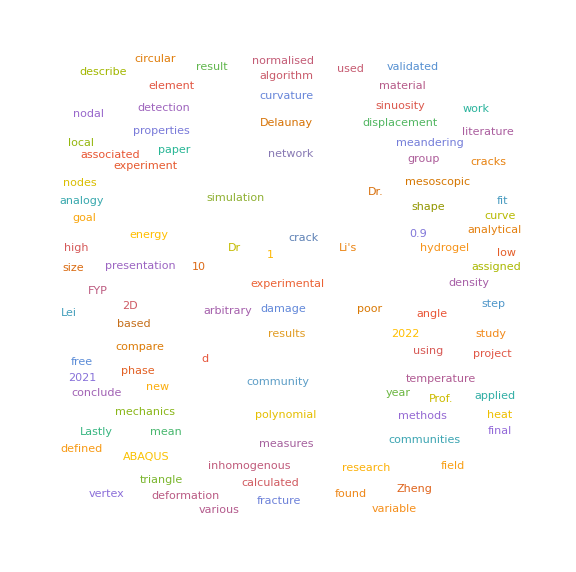

```mathematica
WordCloud[DeleteStopwords[text], ImageSize->Large]
```

```mathematica
CommunityGraphPlot[ResourceFunction["KeywordsGraph"][DeleteStopwords[text],80,VertexSize->"VertexWeight",EdgeStyle->Directive[Black,Dashed,Opacity[0.10]]],CommunityBoundaryStyle->Directive[Red,Dashed,Opacity[0.8]],ImageSize->Full,GraphLayout->"RadialEmbedding"]
```

-Graphics-

```mathematica
CommunityGraphPlot[ResourceFunction["KeywordsGraph"][DeleteStopwords[text],300,VertexSize->"VertexWeight",EdgeStyle->Directive[Black,Dashed,Opacity[0.10]]],CommunityBoundaryStyle->Directive[Red,Dashed,Opacity[0.8]],EdgeStyle->Directive[Black,Dashed,Opacity[0.05]],ImageSize->Full,GraphLayout->"RadialEmbedding"]
```

-Graphics-